Set::write: Tag Times in 2 Null is Protected.

Set::write: Tag Times in 4 Null is Protected.

Set::write: Tag Times in 8 Null is Protected.

General::stop: Further output of Set::write will be suppressed during this calculation.

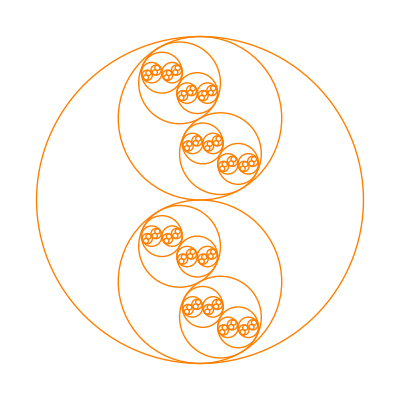

```mathematica
f1[x_,y_,r_,p_] := {x+r/2*Cos[p],y+r/2*Sin[p],r/2,p+angleincr};
f2[x_,y_,r_,p_] := {x-r/2*Cos[p],y-r/2*Sin[p],r/2,p+angleincr};
f3[x_,y_,r_,p_] := {x-r/2*Cos[p],y+r/2*Sin[p],r/2,p+angleincr};
f4[x_,y_,r_,p_] := {x+r/2*Cos[p],y-r/2*Sin[p],r/2,p+angleincr};

numcircles = 2; (*set to 2 or 4*)radius = 20;iter = 6;phase = Pi/2;
angleincr = Pi/6;
(*Print["Phase = ",phase]*)
size = 1+∑_(e=1)^iter numcircles^e;
vals = ConstantArray[0,{size,4}];
vals[[1]] = {0,0,radius,phase};
p=1;
For[i=1, i<iter+1,i++,
chunk = numcircles^(i-1);
lastIndex=1+∑_(e=0)^(i-1) numcircles^e;
(*Print["lastIndex = ",lastIndex];*)
(*p= lastIndex -1*Boole[i-2<=0]- (numcircles^(i-2)-1)*Boole[i-2>0];*)
For[k=lastIndex,k<(lastIndex+numcircles*chunk),k+=numcircles,
(*Print["k is ",k];
Print["p is ",p];*)
If[numcircles==2,
vals[[k]]        = f1[vals[[p,1]],vals[[p,2]],vals[[p,3]],vals[[p,4]]];
vals[[k+1]] = f2[vals[[p,1]],vals[[p,2]],vals[[p,3]],vals[[p,4]]];
, (*otherwise it is 4*)
vals[[k]]        = f1[vals[[p,1]],vals[[p,2]],vals[[p,3]],vals[[p,4]]];
vals[[k+1]] = f2[vals[[p,1]],vals[[p,2]],vals[[p,3]],vals[[p,4]]];
vals[[k+2]] = f2[vals[[p,1]],vals[[p,2]],vals[[p,3]],vals[[p,4]]];
vals[[k+3]] = f2[vals[[p,1]],vals[[p,2]],vals[[p,3]],vals[[p,4]]];
]
p++;
]
p=lastIndex;
]
circles = Table[Circle[{N[vals[[i,1]]],N[vals[[i,2]]]},N[vals[[i,3]]]],{i,size}];Graphics[{Thin,Orange,circles}]

(*{circles = Graphics[{Thin,Orange,Table[Circle[{N[vals[[i,1]]],N[vals[[i,2]]]},N[vals[[i,3]]]],{i,size}]}]}*)

(*temp = fractal[]
Graphics[{Thin,Orange,temp}]*)
(*,{start,0,2Pi},AnimationRunning-> False]*)
```